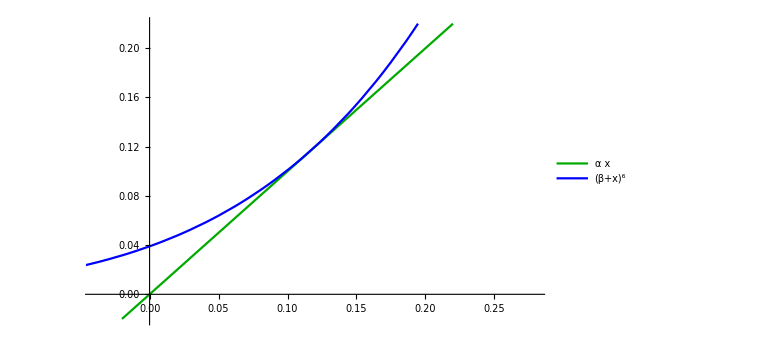

C:\Users\user\Desktop\fg.jpg

```mathematica
f[a_, x_]=a*x;
g[b_, x_]=(b+x)^6;
fg=Plot[
{f[1,x], g[0.582355932, x]}, 
{x, -1, 1}, 
PlotLegends->{α*x, (β+x)^6},
PlotRange->{{-0.04, 0.28}, {-0.02, 0.22}},
PlotStyle->{Darker[Green], Blue},
ImageSize->Large
]
Export["C:\\Users\\user\\Desktop\\fg.jpg", fg]
```